```mathematica
mgmoment=Flatten[Import["mmt_pllndata.dat"]];
dltan=Flatten[Import["occu_pllndata.dat"]];
```

```mathematica
plmgmoment=Table[{n,mgmoment[[n]]},{n,1,Length[mgmoment]}];
pldltan=Table[{n,dltan[[n]]},{n,1,Length[dltan]}];
```

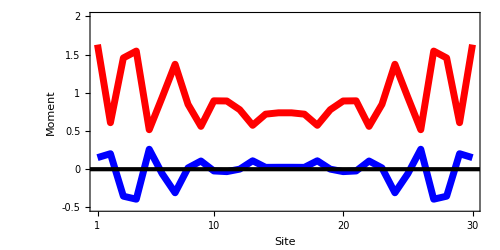

```mathematica
lineplot=ListPlot[{plmgmoment,pldltan},Joined->True,Frame->True,PlotRange->{{1,30},{-0.5,2}},FrameTicks->{{{{-0.5,-0.5,0.018},{0,0,0.018},{0.5,0.5,0.018},{1,1,0.018},{1.5,1.5,0.018},{2,2,0.018}},{{-0.5,Null,0.018},{0,Null,0.018},{0.5,Null,0.018},{1,Null,0.018},{1.5,Null,0.018},{2,Null,0.018}}},{{{1,1,0.018},{10,10,0.018},{20,20,0.018},{30,30,0.018}},
{{1,Null,0.018},{10,Null,0.018},{20,Null,0.018},{30,Null,0.018}}}},GridLines->{None,{0}},
GridLinesStyle->Directive[Thickness[0.006],Black,50],
AspectRatio->0.5,FrameStyle->Directive[Thickness[0.006],Black,25],LabelStyle->{FontFamily->"TimesNewRoman",Black,FontSize->50},
FrameLabel->{{Style["Moment",30,Red,FontFamily->"TimesNewRoman"],Style["δn_i",30,Blue,FontFamily->"TimesNewRoman"]},
{Style["Site",30,FontFamily->"TimesNewRoman"],""}},
PlotStyle->{{Red,Thickness[0.01]},{Blue,Thickness[0.01]}}, ImageSize->500]
Export["line_density_and_moment.eps",lineplot];
```